## Study the sampled parameters

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
transPars=Import["saturationSamplingVaringK.csv"];
pars=Transpose[transPars];
```

```mathematica
us=pars[[Flatten[Position[transPars[[15]],_?(#>0.8&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[19]],_?(0.01<#<0.1&)]]]];
usLowKm2=Flatten[usLow[[RandomInteger[Length[usLow]-1]+1]]];
```

```mathematica
usLowKm2
```

{17.2534,450.934,17.6927,106.865,5.25439,0.148608,0.236667,170.884,86.6245,0.00221059,0.0150061,0.0001,0.1,1,0.818754,0.171653,64003,27.1614,0.0505591,722.045,0.0000255192}

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

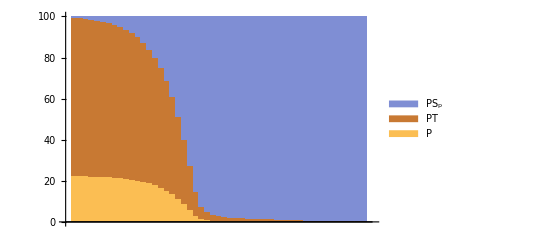

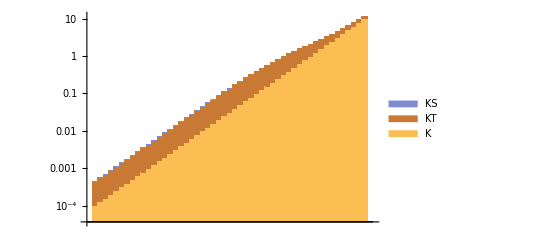

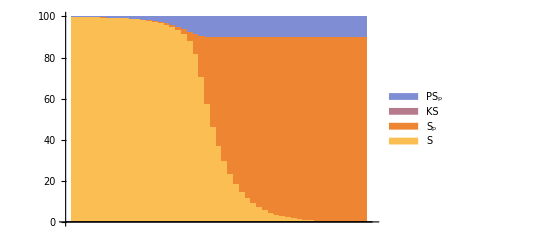

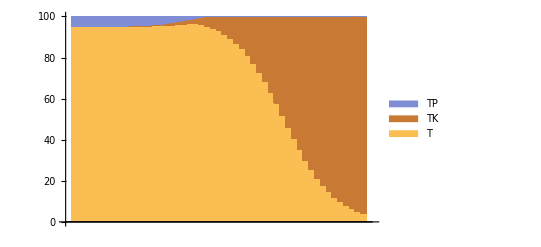

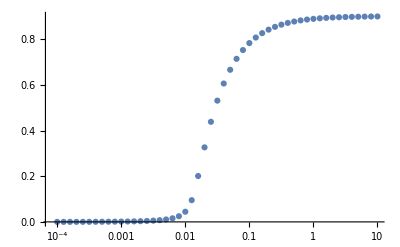

```mathematica
us=pars[[Flatten[Position[transPars[[15]],_?(#>0.8&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[19]],_?(#<0.1&)]]]];
(*usLowKm2=Flatten[usLow[[RandomInteger[Length[usLow]-1]+1]]];*)
usLowKm2={0.16728930764575622,4.836489116236031,61.81648134666554,236.54898459577186,0.865947887108528,0.018744412296491247,10.616834813477592,4.547648424224851,0.0969996161892063,0.0416716178018156,1.5454286263184542,0.0001,0.1,1,0.8592227166246346,0.1608420357668247,29001,398.4293521259751,0.0037399961826800098,0.42834314596774337,0.4296060071055481};

SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};

vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usLowKm2[[Range[10]]]];
Block[{ssthreshold},
totT=usLowKm2[[11]];

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
freet=Evaluate[x[7][ts-0.001]/.sol];
s=Evaluate[x[3][ts-0.001]/.sol];
];
];
];
];
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
BarChart[Transpose[{freet,kt,pt}],ChartLayout->"Percentile",ChartLegends->{"T","TK","TP"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
BarChart[Transpose[{freet,kt,pt}],ChartLayout->"Percentile",ChartLegends->{"T","TK","TP"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

```mathematica
usLowKm2
```

{0.167289,4.83649,61.8165,236.549,0.865948,0.0187444,10.6168,4.54765,0.0969996,0.0416716,1.54543,0.0001,0.1,1,0.859223,0.160842,29001,398.429,0.00374,0.428343,0.429606}

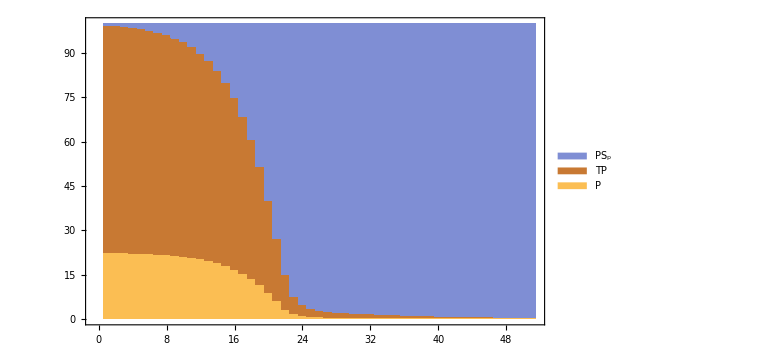

```mathematica
lowPBar=BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","TP","PS_p"},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{False,True,False,False},FrameStyle->{Automatic,Automatic,Automatic,Automatic}]
```

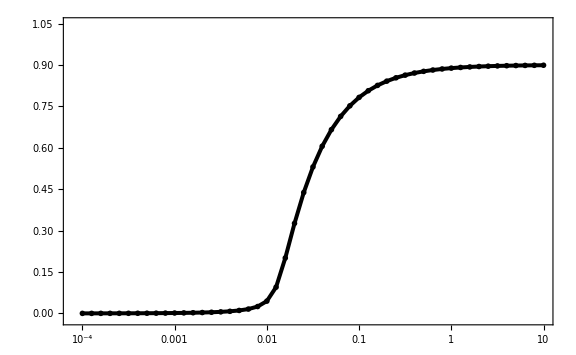

```mathematica
lowOutput1=ListLogLinearPlot[Transpose[{k,x4/totS}],Joined->True, (*PlotLegends->{"S_p"},*)PlotRange->{-0.02,1.05},PlotStyle->{Black,Thickness[0.005]},PlotMarkers->{Automatic, Medium},Ticks->{0,0.5,1},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,False,True,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Black}]
```

```mathematica
lowMechanism1=Overlay[{lowPBar,lowOutput1}]
```

-Graphics--Graphics-

```mathematica
Export["lowKmpUsMechanism1.eps",lowMechanism1];
Export["lowKmpUsMechanism1.pdf",lowMechanism1];
```

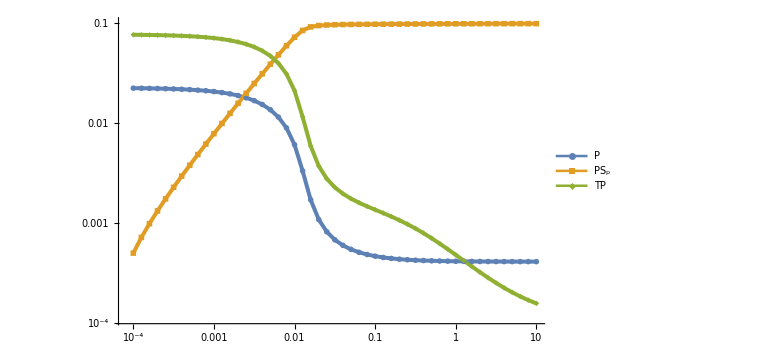

```mathematica
lowAllP = {k,p,psp,pt};
lowPPlot=ListLogLogPlot[Transpose[{lowAllP[[1]],#}]&/@lowAllP[[2;;]],Joined->True,PlotLegends->Placed[{"P","PS_p","TP","KS","S_p"},{0.85,0.65}],(*PlotRange->Automatic,*)PlotMarkers->{Automatic, Medium},PlotStyle->{Thickness[0.005]},Ticks->{Automatic, {{0.0001,""},{0.0005,""},{0.001,"10^-3"},{0.005,""},{0.01,"10^-2"},{0.05,""},{0.1,"10^-1"}}},(*FrameTicks->{{Automatic,Automatic},{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"}},Automatic}},*)LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50(*,Frame->{False,True,False,False}*)(*,FrameStyle->{Automatic,Automatic,Automatic,Automatic}*)]
```

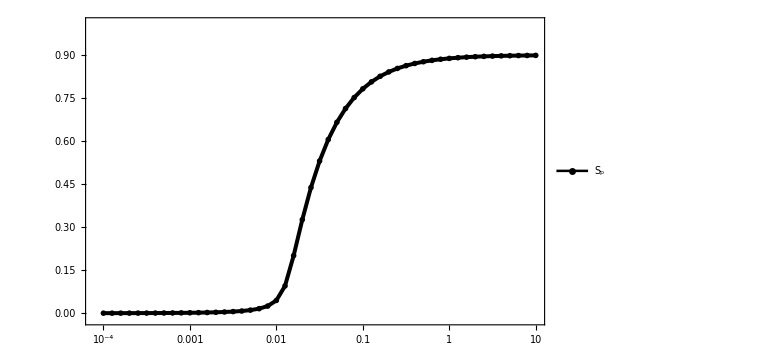

```mathematica
lowOutput=ListLogLinearPlot[Transpose[{k,x4/totS}],Joined->True, PlotLegends->Placed[{"S_p"},{0.835,0.4}],PlotRange->{-0.02,1.01},PlotStyle->{Black,Thickness[0.005]},PlotMarkers->{Automatic, Medium},Ticks->{0,0.5,1},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{False,False,True,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Black}]
```

```mathematica
lowMechanism=Overlay[{lowPPlot,lowOutput}]
```

-Graphics--Graphics-

```mathematica
Export["lowKmpUsMechanism.eps",lowMechanism];
Export["lowKmpUsMechanism.pdf",lowMechanism];
```

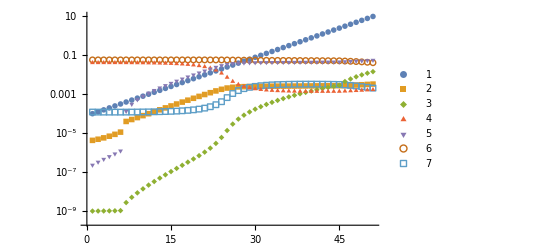

```mathematica
ListLogPlot[{k,ks,kt,p,psp,pt,freet},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

### Now get the dynamics of enzymes in ultrasensitive networks and adaptive network

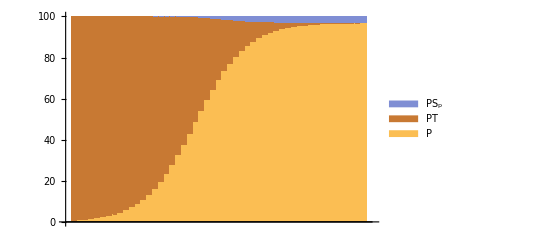

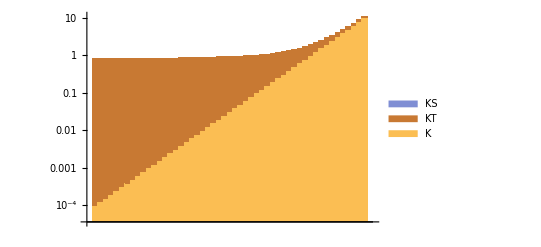

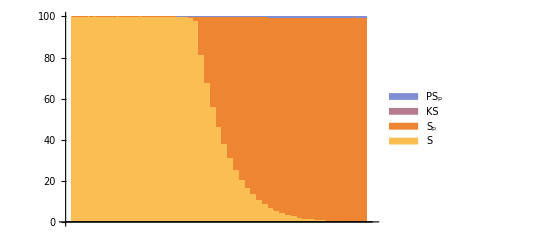

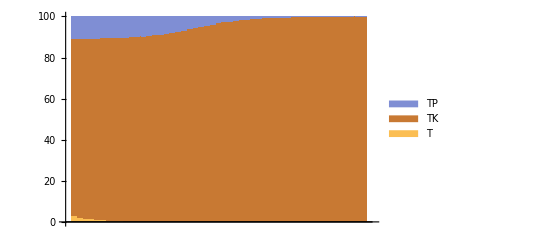

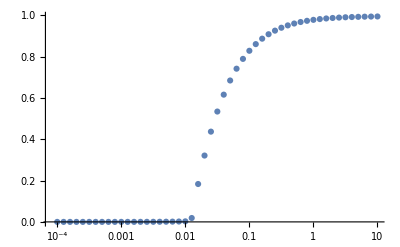

```mathematica
usHigh=us[[Flatten[Position[Transpose[us][[19]],_?(#>10&)]]]];
(*usHighKm2=Flatten[usHigh[[RandomInteger[Length[usHigh]-1]+1]]];*)
usHighKm2={0.0025314890198983395,372.98305430527154,109.77591822580045,0.3086076927929217,9.852927598909943,0.0011839798382625526,494.0030561085748,0.0016621232604372984,91.80635808655883,0.020600646180649555,0.9312099482351888,0.0001,0.1,1,0.9097865641880702,0.08685114363859972,81069,190701.5865905114,31.9308682475404,3.364601169738487*^-6,0.0002243923690037504};

SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};

vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;

Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,10]==usHighKm2[[Range[10]]]];
Block[{ssthreshold},
totT=usHighKm2[[11]];

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
pt=Evaluate[x[9][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
kt=Evaluate[x[8][ts-0.001]/.sol];
freet=Evaluate[x[7][ts-0.001]/.sol];
s=Evaluate[x[3][ts-0.001]/.sol];
k3=usHighKm2[[3]];
k6=usHighKm2[[6]];
k1=usHighKm2[[1]];
k2=usHighKm2[[2]];
k5=usHighKm2[[5]];
k4=usHighKm2[[4]];
k7=usHighKm2[[7]];
k8=usHighKm2[[8]];
k9=usHighKm2[[9]];
k10=usHighKm2[[10]];
];
];
];
];
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
BarChart[Transpose[{freet,kt,pt}],ChartLayout->"Percentile",ChartLegends->{"T","TK","TP"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

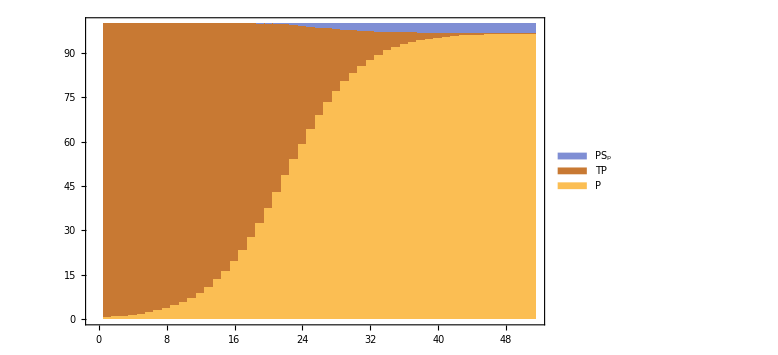

```mathematica
highPBar=BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","TP","PS_p"},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{False,True,False,False},FrameStyle->{Automatic,Automatic,Automatic,Automatic}]
```

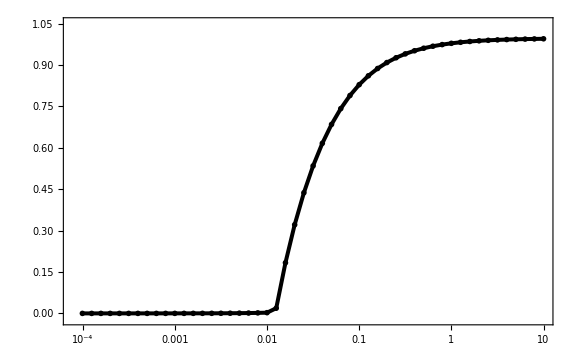

```mathematica
highOutput1=ListLogLinearPlot[Transpose[{k,x4/totS}],Joined->True, (*PlotLegends->{"S_p"},*)PlotRange->{-0.02,1.05},PlotStyle->{Black,Thickness[0.005]},PlotMarkers->{Automatic, Medium},Ticks->{0,0.5,1},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,False,True,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Black}]
```

```mathematica
highMechanism1=Overlay[{highPBar,highOutput1}]
```

-Graphics--Graphics-

```mathematica
Export["highKmpUsMechanism1.eps",highMechanism1];
Export["highKmpUsMechanism1.pdf",highMechanism1];
```

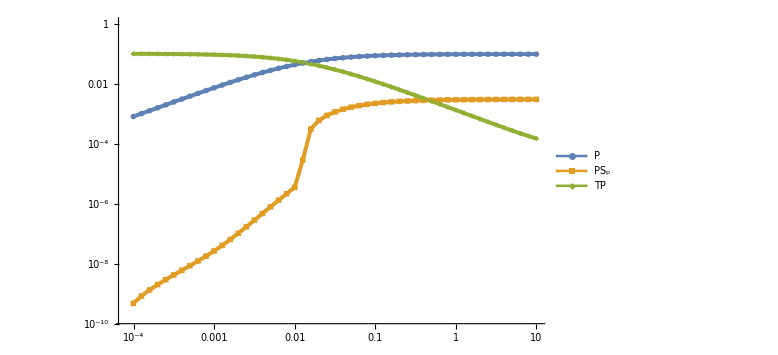

```mathematica
highAllP = {k,p,psp,pt};
highPPlot=ListLogLogPlot[Transpose[{highAllP[[1]],#}]&/@highAllP[[2;;]],Joined->True,PlotLegends->Placed[{"P","PS_p","TP","KS","S_p"},{0.85,0.35}],(*PlotRange->Automatic,*)PlotMarkers->{Automatic, Medium},PlotStyle->{Thickness[0.005]},Ticks->{Automatic, Automatic(*{{0.0001,""},{0.0005,""},{0.001,"10^-3"},{0.005,""},{0.01,"10^-2"},{0.05,""},{0.1,"10^-1"}}*)},(*FrameTicks->{{Automatic,Automatic},{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"}},Automatic}},*)LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50(*,Frame->{False,True,False,False}*)(*,FrameStyle->{Automatic,Automatic,Automatic,Automatic}*)]
```

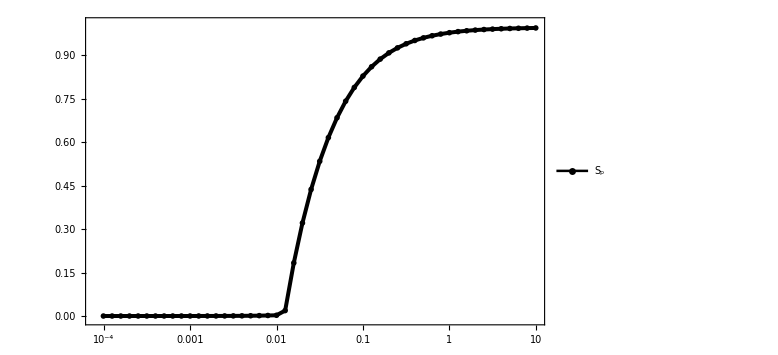

```mathematica
highOutput=ListLogLinearPlot[Transpose[{k,x4/totS}],Joined->True, PlotLegends->Placed[{"S_p"},{0.835,0.1}],PlotRange->{-0.01,1.01},PlotStyle->{Black,Thickness[0.005]},PlotMarkers->{Automatic, Medium},Ticks->{0,0.5,1},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{False,False,True,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Black}]
```

```mathematica
highMechanism=Overlay[{highPPlot,highOutput}]
```

-Graphics--Graphics-

```mathematica
Export["highKmpUsMechanism.eps",highMechanism];
Export["highKmpUsMechanism.pdf",highMechanism];
```

## TEST

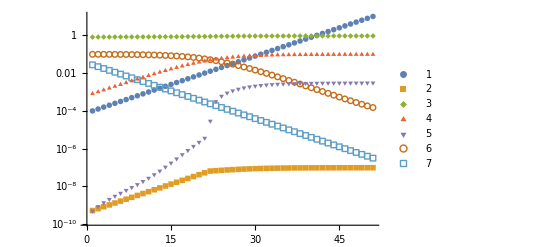

```mathematica
ListLogPlot[{k,ks,kt,p,psp,pt,freet},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

```mathematica
allP = {k,p,psp,pt};
```

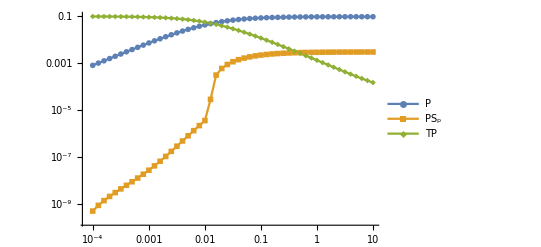

```mathematica
ListLogLogPlot[Transpose[{allP[[1]],#}]&/@allP[[2;;]],Joined->True,PlotLegends->{"P","PS_p","TP","KS","S_p"},PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

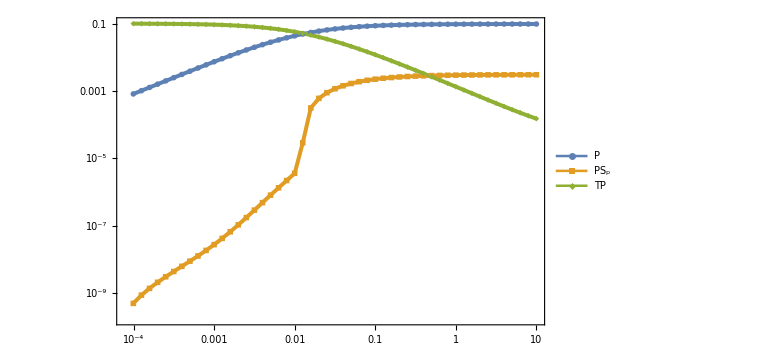

```mathematica
pPlot=ListLogLogPlot[Transpose[{allP[[1]],#}]&/@allP[[2;;]],Joined->True,PlotLegends->Placed[{"P","PS_p","TP","KS","S_p"},{0.85,0.35}],PlotRange->Full,PlotMarkers->{Automatic, Medium},PlotStyle->{(*Blue,Dashed,*)Thickness[0.005]},Ticks->{},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Automatic,Automatic,Automatic}]
```

```mathematica
output=ListLogLinearPlot[Transpose[{k,x4/totS}],Joined->True, PlotLegends->Placed[{"S_p"},{0.835,0.1}],PlotRange->{-0.01,1.01},PlotStyle->{Black,Thickness[0.005]},PlotMarkers->{Automatic, Medium},Ticks->{0,0.5,1},LabelStyle->{20,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{False,False,True,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Black}]
```

-Graphics-

```mathematica
pAndOutPlot=Overlay[{output,pPlot}]
```

-Graphics--Graphics-

```mathematica
Export["highKmpUsMechanism.eps",pAndOutPlot];
Export["highKmpUsMechanism.pdf",pAndOutPlot];
```

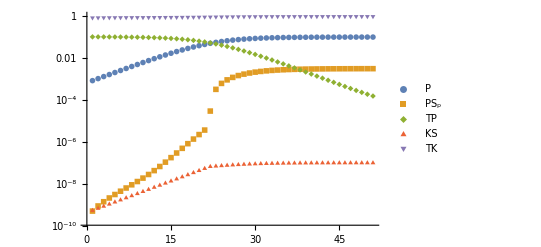

```mathematica
ListLogPlot[{p,psp,pt,ks,kt},PlotLegends->{"P","PS_p","TP","KS","TK"},PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

```mathematica
usHighKm2
```

{0.00253149,372.983,109.776,0.308608,9.85293,0.00118398,494.003,0.00166212,91.8064,0.0206006,0.93121,0.0001,0.1,1,0.909787,0.0868511,81069,190702.,31.9309,3.3646×10^-6,0.000224392}

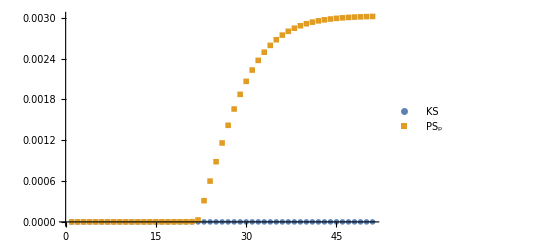

```mathematica
ListPlot[{ks,psp},PlotLegends->{"KS","PS_p"},PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

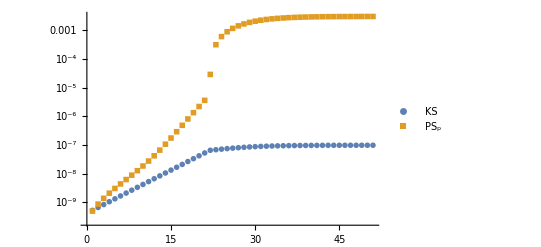

```mathematica
ListLogPlot[{ks,psp},PlotLegends->{"KS","PS_p"},PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

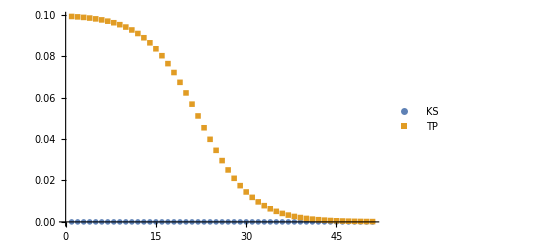

```mathematica
ListPlot[{ks,pt},PlotLegends->{"KS","TP"},PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

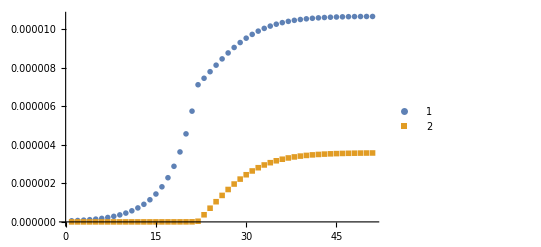

```mathematica
ListPlot[{ks*k3,psp*k6},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

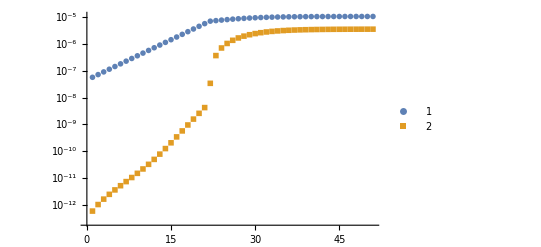

```mathematica
ListLogPlot[{ks*k3,psp*k6},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

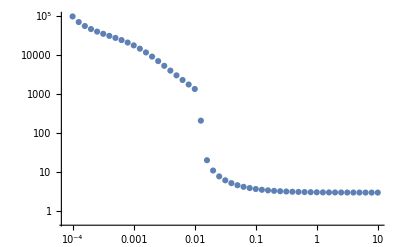

```mathematica
ListLogLogPlot[Transpose[{k,(ks*k3)/(psp*k6)}]]
```

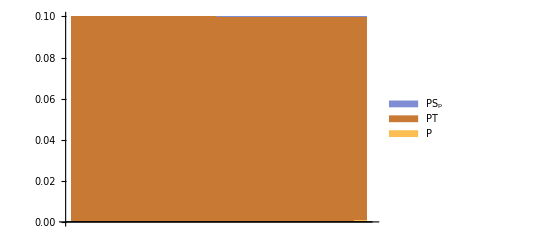

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Stacked",ChartLegends->{"P","PT","PS_p"}]
```

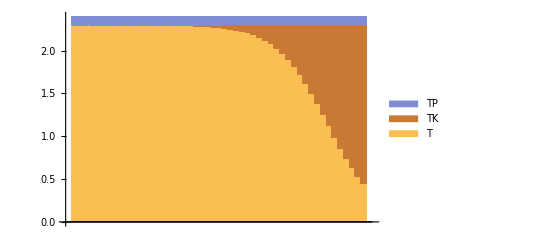

```mathematica
BarChart[Transpose[{freet,kt,pt}],ChartLayout->"Stacked",ChartLegends->{"T","TK","TP"}]
```

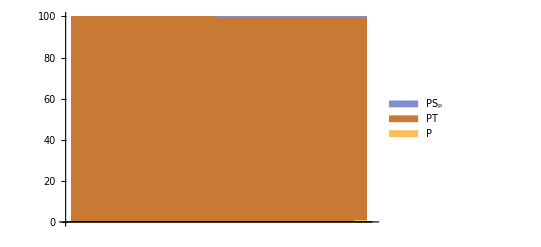

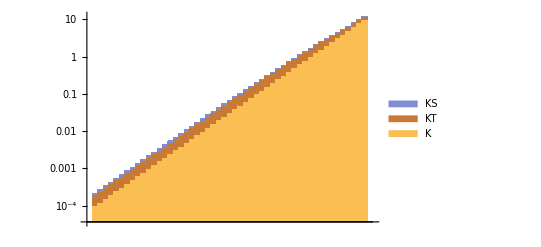

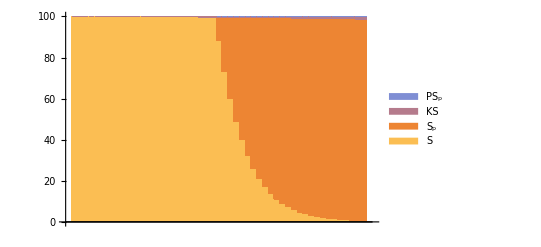

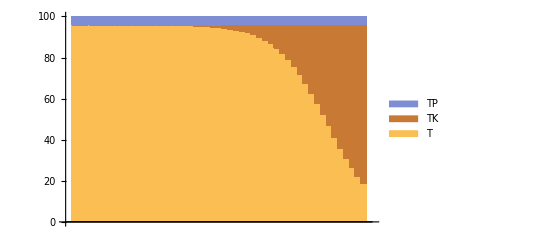

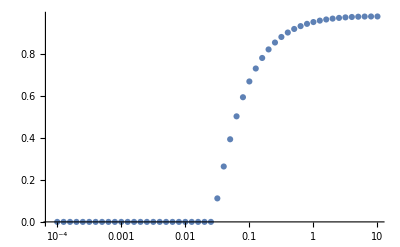

```mathematica
BarChart[Transpose[{p,pt,psp}],ChartLayout->"Percentile",ChartLegends->{"P","PT","PS_p"}]
BarChart[Transpose[{k,kt,ks}],ChartLayout->"Stacked",ChartLegends->{"K","KT","KS"},ScalingFunctions->"Log"]
BarChart[Transpose[{s,x4,ks,psp}],ChartLayout->"Percentile",ChartLegends->{"S","S_p","KS","PS_p"}]
BarChart[Transpose[{freet,kt,pt}],ChartLayout->"Percentile",ChartLegends->{"T","TK","TP"}]
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

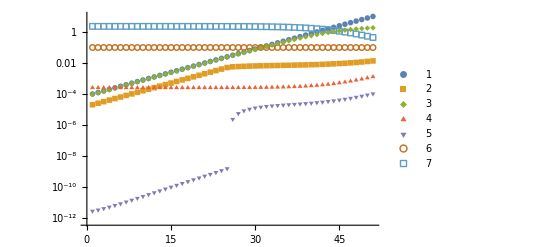

```mathematica
ListLogPlot[{k,ks,kt,p,psp,pt,freet},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

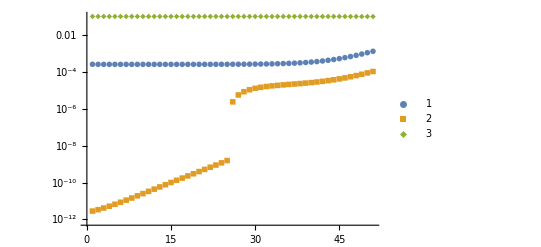

```mathematica
ListLogPlot[{p,psp,pt},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```

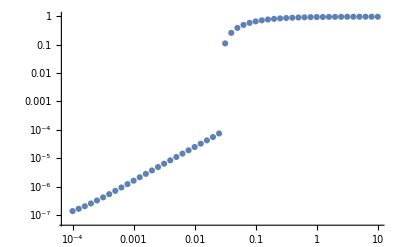

```mathematica
ListLogLogPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```

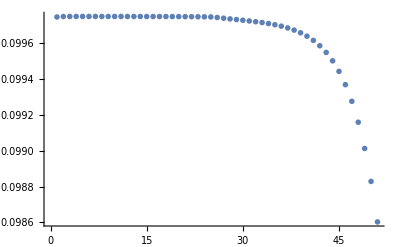

```mathematica
ListPlot[{pt},PlotLegends->Automatic,PlotRange->Full,PlotStyle->Thick,PlotMarkers->{Automatic, Medium}]
```